X_cm=(m_1 x_1+m_2 x_2+m_3 x_3+m_4 x_4)/(m_1+m_2+m_3+m_4)

ρ_1^(12)=x_1-x_2

ρ_2^(12)=x_3-x_4

ρ_3^(12)=(m_1 x_1+m_2 x_2)/(m_1+m_2)-(m_3 x_3+m_4 x_4)/(m_3+m_4)

and mass-scaled Jacobi coordinates as:

y_1^(12)=√(μ_12/μ)(x_1-x_2)

y_2^(12)=√(μ_34/μ)(x_3-x_4)

y_3^(12)=√((μ_(12,34))/μ)((m_1 x_1+m_2 x_2)/(m_1+m_2)-(m_3 x_3+m_4 x_4)/(m_3+m_4))

y_4^(12)=√(M/μ)X_cm

The convention here is that the superscript (12) indicates this coordinate system is convenient for treating the interaction between particles 1 and 2.  In matrix notation:

(y_1^(12)
y_2^(12)
y_3^(12)
y_4^(12))=1/(√μ)(√μ_12 | -√μ_12 | 0 | 0
0 | 0 | √μ_34 | -√μ_34
(√(μ_(12,34))m_1)/(m_1+m_2) | (√(μ_(12,34))m_2)/(m_1+m_2) | -(√(μ_(12,34))m_3)/(m_3+m_4) | -(√(μ_(12,34))m_4)/(m_3+m_4)
m_1/(√M) | m_2/(√M) | m_3/(√M) | m_4/(√M))(x_1
x_2
x_3
x_4)

Now we define the hyperspherical coordinates as:

y_1^(12)=cos θ_12

y_2^(12)=sin θ_12 cos ϕ_12

y_3^(12)=sin θ_12 sin ϕ_12

```mathematica
Clear[μ4]
```

```mathematica
μ4=(μ12 μ34 μ1234)^(1/3)/.{μ12->((m1 m2)/(m1+m2)),μ34->((m3 m4)/(m3+m4)),μ1234->(((m1+m2)(m3+m4))/(m1+m2+m3+m4)),M->m1+m2+m3+m4}
```

((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/3)

```mathematica
A=1/(√μ4)({{√μ12, -√μ12, 0, 0}, {0, 0, √μ34, -√μ34}, {(√μ1234 m1)/(m1+m2), (√μ1234 m2)/(m1+m2), -(√μ1234 m3)/(m3+m4), -(√μ1234 m4)/(m3+m4)}, {m1/(√M), m2/(√M), m3/(√M), m4/(√M)}})/.{μ12->((m1 m2)/(m1+m2)),μ34->((m3 m4)/(m3+m4)),μ1234->(((m1+m2)(m3+m4))/(m1+m2+m3+m4)),M->m1+m2+m3+m4}//FullSimplify
```

{{(√((m1 m2)/(m1+m2)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6),-(√((m1 m2)/(m1+m2)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6),0,0},{0,0,(√((m3 m4)/(m3+m4)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6),-(√((m3 m4)/(m3+m4)))/((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)},{(m1 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m1+m2) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)),(m2 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m1+m2) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)),-(m3 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m3+m4) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6)),-(m4 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)))/((m3+m4) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6))},{m1/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4)),m2/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4)),m3/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4)),m4/(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) √(m1+m2+m3+m4))}}

```mathematica
xsol=Simplify[Solve[({{x}, {y}, {z}, {XCM}})==A.({{x1}, {x2}, {x3}, {x4}}),{x1,x2,x3,x4}],{mup>0,mdn>0}][[1]]
```

{x1→((m3+m4) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) (m1 m2 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) x+m2 (m2 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) x+m3 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) x+m4 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) x+√((m1 m2)/(m1+m2)) √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) √(m1+m2+m3+m4) XCM+√((m1 m2)/(m1+m2)) m3 z+√((m1 m2)/(m1+m2)) m4 z)+m1 √((m1 m2)/(m1+m2)) (√(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) √(m1+m2+m3+m4) XCM+(m3+m4) z)))/(√((m1 m2)/(m1+m2)) (((m1+m2) (m3+m4))/(m1+m2+m3+m4))^(3/2) (m1+m2+m3+m4)^2),x2→((m3+m4) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) (-m1^2 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) x+m1 (-m2 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) x-m3 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) x-m4 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) x+√((m1 m2)/(m1+m2)) √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) √(m1+m2+m3+m4) XCM+√((m1 m2)/(m1+m2)) m3 z+√((m1 m2)/(m1+m2)) m4 z)+m2 √((m1 m2)/(m1+m2)) (√(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) √(m1+m2+m3+m4) XCM+(m3+m4) z)))/(√((m1 m2)/(m1+m2)) (((m1+m2) (m3+m4))/(m1+m2+m3+m4))^(3/2) (m1+m2+m3+m4)^2),x3→((m1+m2) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) (m3 √((m3 m4)/(m3+m4)) √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) √(m1+m2+m3+m4) XCM+m3 m4 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) y-(m1+m2) m3 √((m3 m4)/(m3+m4)) z+m4 (√((m3 m4)/(m3+m4)) √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) √(m1+m2+m3+m4) XCM+m1 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) y+m2 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) y+m4 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) y-m1 √((m3 m4)/(m3+m4)) z-m2 √((m3 m4)/(m3+m4)) z)))/(√((m3 m4)/(m3+m4)) (((m1+m2) (m3+m4))/(m1+m2+m3+m4))^(3/2) (m1+m2+m3+m4)^2),x4→-(((m1+m2) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) (m3^2 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) y+m4 √((m3 m4)/(m3+m4)) (-√(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) √(m1+m2+m3+m4) XCM+(m1+m2) z)+m3 (-√((m3 m4)/(m3+m4)) √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) √(m1+m2+m3+m4) XCM+m1 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) y+m2 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) y+m4 √(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) y+m1 √((m3 m4)/(m3+m4)) z+m2 √((m3 m4)/(m3+m4)) z)))/(√((m3 m4)/(m3+m4)) (((m1+m2) (m3+m4))/(m1+m2+m3+m4))^(3/2) (m1+m2+m3+m4)^2))}

```mathematica
Clear[R]
```

```mathematica
x12=Simplify[x1-x2/.xsol];FullSimplify[x12,{m1>0,m2>0,m3>0,m4>0}]
```

(√(m1+m2) ((m3 m4)/(m1+m2+m3+m4))^(1/6) x)/(m1 m2)^(1/3)

```mathematica
x12hyp=Simplify[x12]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x12hyp,{mdn>0,mup>0}]
```

(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) R Cos[ϕ] Sin[θ])/(√((m1 m2)/(m1+m2)))

```mathematica
x13=FullSimplify[x1-x3/.xsol,{m1>0,m2>0,m3>0,m4>0}]
```

1/((m1+m2) (m3+m4) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/3))(m1 (-m4 √((m1 m2 (m3+m4))/(m1+m2+m3+m4)) y+m3 √((m1 m2 m3 m4)/((m1+m2) (m3+m4))) z+m4 √((m1 m2 m3 m4)/((m1+m2) (m3+m4))) z)+m2 (m3 √(((m1+m2) m3 m4)/(m1+m2+m3+m4)) x+m4 √(((m1+m2) m3 m4)/(m1+m2+m3+m4)) x-m4 √((m1 m2 (m3+m4))/(m1+m2+m3+m4)) y+m3 √((m1 m2 m3 m4)/((m1+m2) (m3+m4))) z+m4 √((m1 m2 m3 m4)/((m1+m2) (m3+m4))) z))

```mathematica
x13hyp=Simplify[x13]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x13hyp]
```

(R ((m1 m2 m3 m4 Cos[θ])/(√((m1 m2 m3 m4)/((m1+m2) (m3+m4))))+Sin[θ] (m2 (m3+m4) √(((m1+m2) m3 m4)/(m1+m2+m3+m4)) Cos[ϕ]-(m1+m2) m4 √((m1 m2 (m3+m4))/(m1+m2+m3+m4)) Sin[ϕ])))/((m1+m2) (m3+m4) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/3))

```mathematica
x14=FullSimplify[x1-x4/.xsol,{m1>0,m2>0,m3>0,m4>0}]
```

1/((m1+m2) (m3+m4) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/3))(m1 (m3 √((m1 m2 (m3+m4))/(m1+m2+m3+m4)) y+m3 √((m1 m2 m3 m4)/((m1+m2) (m3+m4))) z+m4 √((m1 m2 m3 m4)/((m1+m2) (m3+m4))) z)+m2 (m3 √(((m1+m2) m3 m4)/(m1+m2+m3+m4)) x+m4 √(((m1+m2) m3 m4)/(m1+m2+m3+m4)) x+m3 √((m1 m2 (m3+m4))/(m1+m2+m3+m4)) y+m3 √((m1 m2 m3 m4)/((m1+m2) (m3+m4))) z+m4 √((m1 m2 m3 m4)/((m1+m2) (m3+m4))) z))

```mathematica
x14hyp=Simplify[x14]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x14hyp]
```

(R ((m1 m2 m3 m4 Cos[θ])/(√((m1 m2 m3 m4)/((m1+m2) (m3+m4))))+Sin[θ] (m2 (m3+m4) √(((m1+m2) m3 m4)/(m1+m2+m3+m4)) Cos[ϕ]+(m1+m2) m3 √((m1 m2 (m3+m4))/(m1+m2+m3+m4)) Sin[ϕ])))/((m1+m2) (m3+m4) ((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/3))

```mathematica
x23hyp=Simplify[x2-x3/.xsol]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x23hyp]
```

(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) R (√(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) (m1+m2+m3+m4) Cos[θ]-(m1 (m3+m4) Cos[ϕ] Sin[θ])/(√((m1 m2)/(m1+m2)))-((m1+m2) m4 Sin[θ] Sin[ϕ])/(√((m3 m4)/(m3+m4)))))/((m1+m2) (m3+m4))

```mathematica
x24hyp=Simplify[x2-x4/.xsol]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x24hyp]
```

(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) R (√(((m1+m2) (m3+m4))/(m1+m2+m3+m4)) (m1+m2+m3+m4) Cos[θ]-(m1 (m3+m4) Cos[ϕ] Sin[θ])/(√((m1 m2)/(m1+m2)))+((m1+m2) m3 Sin[θ] Sin[ϕ])/(√((m3 m4)/(m3+m4)))))/((m1+m2) (m3+m4))

```mathematica
x34hyp=Simplify[x3-x4/.xsol]/.{x->R Sin[θ]Cos[ϕ],y->R Sin[θ]Sin[ϕ],z->R Cos[θ]};FullSimplify[x34hyp]
```

(((m1 m2 m3 m4)/(m1+m2+m3+m4))^(1/6) R Sin[θ] Sin[ϕ])/(√((m3 m4)/(m3+m4)))

```mathematica
equalmassxij=FullSimplify[{x12hyp,x13hyp,x14hyp,x23hyp,x24hyp,x34hyp}/.{m1->1,m2->1,m3->1,m4->1}]
```

{2^(1/6) R Cos[ϕ] Sin[θ],(R (√2 Cos[θ]+Sin[θ] (Cos[ϕ]-Sin[ϕ])))/2^(5/6),(R (√2 Cos[θ]+Sin[θ] (Cos[ϕ]+Sin[ϕ])))/2^(5/6),(R (√2 Cos[θ]-Sin[θ] (Cos[ϕ]+Sin[ϕ])))/2^(5/6),(R (√2 Cos[θ]+Sin[θ] (-Cos[ϕ]+Sin[ϕ])))/2^(5/6),2^(1/6) R Sin[θ] Sin[ϕ]}

```mathematica
equalmassxij[[1]]==0/.R->1
```

2^(1/6) Cos[ϕ] Sin[θ]==0

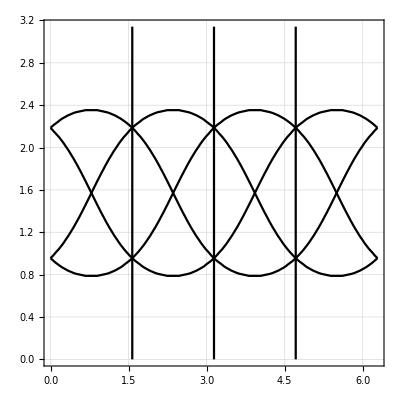

```mathematica
ContourPlot[Evaluate[equalmassxij==0/.R->1],{ϕ,0,2π},{θ,0,π},GridLines->Automatic]
```

```mathematica
unequalmassxij=FullSimplify[{x12hyp,x13hyp,x14hyp,x23hyp,x24hyp,x34hyp}/.{m1->1,m2->1,m3->α,m4->α,R->1,θ->t π,ϕ->f π}]
```

{2^(1/3) (α^2/(1+α))^(1/6) Cos[f π] Sin[π t],(√α Cos[π t]+(√(α^2/(1+α)) Cos[f π]-√(α/(1+α)) Sin[f π]) Sin[π t])/(2^(2/3) (α^2/(1+α))^(1/3)),(√α Cos[π t]+(√(α^2/(1+α)) Cos[f π]+√(α/(1+α)) Sin[f π]) Sin[π t])/(2^(2/3) (α^2/(1+α))^(1/3)),((α^2/(1+α))^(1/6) (√(1+α) Cos[π t]-(√α Cos[f π]+Sin[f π]) Sin[π t]))/(2^(2/3) √α),((α^2/(1+α))^(1/6) (√(1+α) Cos[π t]+(-√α Cos[f π]+Sin[f π]) Sin[π t]))/(2^(2/3) √α),(2^(1/3) (α^2/(1+α))^(1/6) Sin[f π] Sin[π t])/(√α)}

```mathematica
c12=ContourPlot[Evaluate[unequalmassxij[[1]]==0/.{R->1,α->1}],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Black,FrameLabel->{"ϕ/π","θ/π"}];c13=ContourPlot[Evaluate[unequalmassxij[[2]]==0/.{R->1,α->1}],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Red,FrameLabel->{"ϕ/π","θ/π"}];
c14=ContourPlot[Evaluate[unequalmassxij[[3]]==0/.{R->1,α->1}],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Blue,FrameLabel->{"ϕ/π","θ/π"}];
c23=ContourPlot[Evaluate[unequalmassxij[[4]]==0/.{R->1,α->1}],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Green,FrameLabel->{"ϕ/π","θ/π"}];
c24=ContourPlot[Evaluate[unequalmassxij[[5]]==0/.{R->1,α->1}],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Orange,FrameLabel->{"ϕ/π","θ/π"}];
c34=ContourPlot[Evaluate[unequalmassxij[[6]]==0/.{R->1,α->1}],{f,-0.1,2.1},{t,0,1},GridLines->Automatic,ContourStyle->Yellow,FrameLabel->{"ϕ/π","θ/π"}];
```

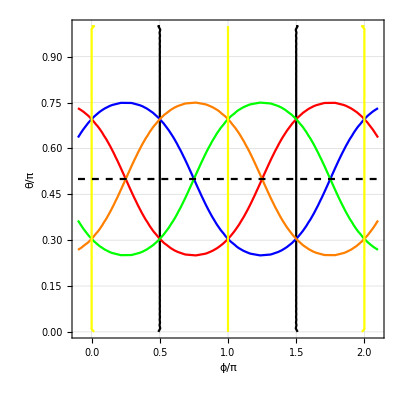

```mathematica
Show[{c12,c13,c14,c23,c24,c34},Plot[0.5,{x,-.1,2.1},PlotStyle->Dashed]]
```

```mathematica
cptable=Table[ContourPlot[Evaluate[unequalmassxij[[i]]==0/.{R->1,α->1}],{f,0,.5},{t,0,.5},GridLines->Automatic,ContourStyle->Black],{i,1,6}];
```

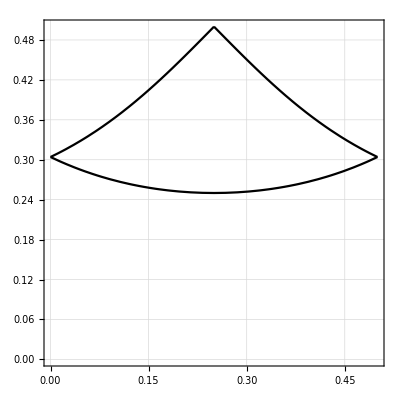

```mathematica
Show[cptable]
```

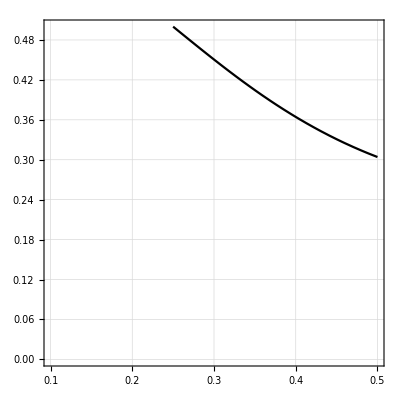
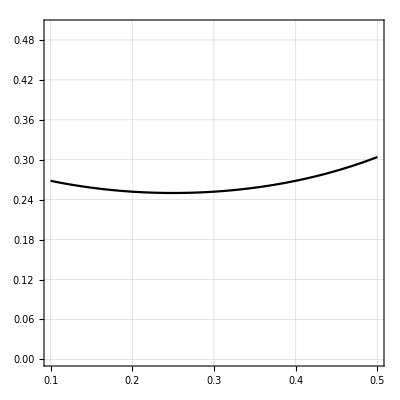
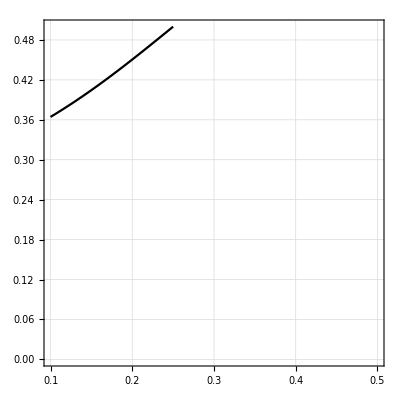
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ContourPlot[Evaluate[unequalmassxij[[i]]==0/.{R->1,α->1}],{f,.5,.1},{t,0,.5},GridLines->Automatic],{i,1,6}]
```

The potential energy

V(x,y,z)=V_2(x_12)+V_2(x_23)+V_2(x_13)+V_2(x_24)+V_2(x_14)+V_2(x_34) + 1/2 μ ω^2(x^2+y^2+z^2)

4-body boundary conditions for the up-up-down-down problem are

Ψ(x=0,y,z)=0

Ψ(x,y=0,z)=0

Ψ(x,y,z)=±Ψ(x,y,-z)             (+ for positive parity, and - for negative parity)

Ψ(r→big)=0

### Matrix elements of the kinetic energy

The angular kinetic energy operator is

-ℏ^2/(2μ R^2)(1/(sin θ)∂/(∂θ)sin θ ∂/(∂θ) + 1/(sin^2 θ)∂^2/(∂ϕ^2))

Let the basis functions be separable of the form u_i(ϕ)v_j(θ) and calculate

H_(i'j', i j)=-ℏ^2/(2μ R^2)∫u_i(ϕ)v_j(θ)(1/(sin θ)∂/(∂θ)sin θ ∂/(∂θ) + 1/(sin^2 θ)∂^2/(∂ϕ^2))u_i'(ϕ)v_j'(θ) sin θ ⅆθ ⅆϕ

H_(i'j', i j)=-ℏ^2/(2μ R^2)∫u_i(ϕ)v_j(θ)((u_i'(ϕ))/(sin θ)∂/(∂θ)sin θ (∂v_j'(θ))/(∂θ) + (v_j'(θ))/(sin^2 θ)(∂^2 u_i'(ϕ))/(∂ϕ^2)) sin θ ⅆθ ⅆϕ

H_(i'j', i j)=-ℏ^2/(2μ R^2)(∫(u_i(ϕ)u_i'(ϕ)(v_j(θ))/(sin θ)∂/(∂θ)sin θ (∂v_j'(θ))/(∂θ) +v_j(θ) (v_j'(θ))/(sin^2 θ)u_i'(ϕ)(∂^2 u_i'(ϕ))/(∂ϕ^2))) sin θ ⅆθ ⅆϕ

H_(i'j', i j)=-ℏ^2/(2μ R^2)((∫u_i(ϕ)u_i'(ϕ) ⅆϕ∫(v_j(θ))/(sin θ)∂/(∂θ)sin θ (∂v_j'(θ))/(∂θ)sin θ ⅆθ +∫v_j(θ) (v_j'(θ))/(sin^2 θ)sin θ ⅆθ∫u_i(ϕ)(∂^2 u_i'(ϕ))/(∂ϕ^2) ⅆϕ))

H_(i'j', i j)=-ℏ^2/(2μ R^2)(∫u_i(ϕ)u_i'(ϕ) ⅆϕ∫v_j(θ)∂/(∂θ)sin θ (∂v_j'(θ))/(∂θ) ⅆθ +∫v_j(θ) (v_j'(θ))/(sin θ) ⅆθ∫u_i(ϕ)(∂^2 u_i'(ϕ))/(∂ϕ^2) ⅆϕ)

H_(i'j', i j)=-ℏ^2/(2μ R^2)(∫u_i(ϕ)u_i'(ϕ) ⅆϕ∫v_j(θ)(sin θ (∂^2 v_j'(θ))/(∂θ^2)+cos θ (∂v_j'(θ))/(∂θ) )ⅆθ +∫v_j(θ) (v_j'(θ))/(sin θ) ⅆθ∫u_i(ϕ)(∂^2 u_i'(ϕ))/(∂ϕ^2) ⅆϕ)

```mathematica
FullSimplify[Cos[ArcTan[y]]]
```

1/(√(1+y^2))

```mathematica
6.21 10^-4 3600
```

2.2356

```mathematica
60/2.24
```

26.7857

### representations of other permutation operators

First, let’s define the Jacobi set we’ve been working with as (y⃗)^(12):

(y⃗)^(12)=S_12 x⃗

where:

S_12=1/(√μ)(√μ_12 | -√μ_12 | 0 | 0
0 | 0 | √μ_34 | -√μ_34
(√(μ_(12,34))m_1)/(m_1+m_2) | (√(μ_(12,34))m_2)/(m_1+m_2) | -(√(μ_(12,34))m_3)/(m_3+m_4) | -(√(μ_(12,34))m_4)/(m_3+m_4)
m_1/(√M) | m_2/(√M) | m_3/(√M) | m_4/(√M))

The corresponding Jacobi set with, for instance 13 coupled together into the first Jacobi vector would be obtained by operating on y^(13)=𝒫_23 y^(12) where

𝒫_23=S_12 P_23 S_12^-1

where

P_23=(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)

acts as

(x_1
x_3
x_2
x_4)=(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)(x_1
x_2
x_3
x_4)

1/(√μ)(√μ_13 | -√μ_13 | 0 | 0
0 | 0 | √μ_24 | -√μ_24
(√(μ_(13,24))m_1)/(m_1+m_3) | (√(μ_(13,24))m_2)/(m_1+m_3) | -(√(μ_(13,24))m_3)/(m_2+m_4) | -(√(μ_(12,24))m_4)/(m_2+m_4)
m_1/(√M) | m_2/(√M) | m_3/(√M) | m_4/(√M))(x_1
x_3
x_2
x_4)=1/(√μ)(√μ_13 | -√μ_13 | 0 | 0
0 | 0 | √μ_24 | -√μ_24
(√(μ_(13,24))m_1)/(m_1+m_3) | (√(μ_(13,24))m_2)/(m_1+m_3) | -(√(μ_(13,24))m_3)/(m_2+m_4) | -(√(μ_(12,24))m_4)/(m_2+m_4)
m_1/(√M) | m_2/(√M) | m_3/(√M) | m_4/(√M))(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)(x_1
x_2
x_3
x_4)

y^(13)=S_13 P_23 x

y^(12)=S_12 x=S_12 P_23^-1 S_13^-1 y^(13)

y^(12)=S_12 P_23^-1 S_13^-1 y^(13)

y^(13)=S_13 P_23 S_12^-1 y^(12)

𝒫_23=S_13 P_23 S_12^-1

when translated to hyperspherical (i.e. spherical polar in this case) coordinates looks like

(y_1^(13)
y_2^(13)
y_3^(13))=(√(μ_13/μ)(x_1-x_3)
√(μ_23/μ)(x_3-x_2)
□)=(R sin θ_13 cos ϕ_13
R sin θ_13 sin ϕ_13
R cos θ_13)=𝒫_23 (R sin θ_12 cos ϕ_12
R sin θ_12 sin ϕ_12
R cos θ_12)=

Then